### Trying to understand data discrepancies

What data are we dropping

From GoL-10-Data:

### Video looping

```mathematica
vid = AnimationVideo[ArrayPlot[CellularAutomaton["GameOfLife",{$LifeData["Gosper glider gun"]["MatrixData"], 0}, {{{i}}, {-5, 35}, {-5, 45}}], Mesh->True,MeshStyle->Opacity[.05],ImageSize->250], {i, 101, 131, 1}];
```

```mathematica
s = VideoPlay[vid, Looping->True];
Dynamic[s["CurrentFrame"]]
```

### Test factorability by compressing the graphs. Any edges that don’t branch get removed and then we just test the area of each rectangle

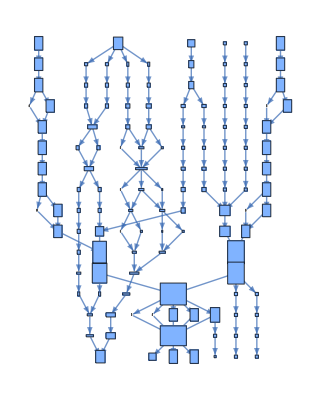

```mathematica
BoundingBoxLayeredGraph[$LifeData["Period-15 glider gun"]]
```

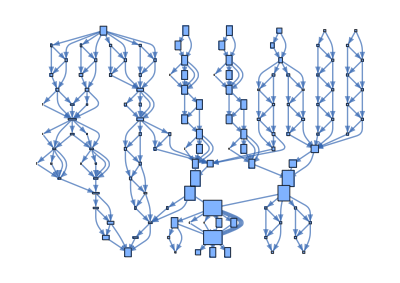

```mathematica
Function[g, Module[{vertices,edges,newEdges, toRemove},vertices=VertexList[g];
toRemove=Select[vertices,(VertexInDegree[g,#]==1&&VertexOutDegree[g,#]==1)&];newEdges=Flatten[Table[With[{in=First[Select[EdgeList[g],Last[#]==v&]],out=First[Select[EdgeList[g],First[#]==v&]]},If[in=!=Missing["NotAvailable"]&&out=!=Missing["NotAvailable"],{First[in]->Last[out]},{}]],{v,toRemove}],1];LayeredGraph[Complement[EdgeList[g],EdgeList[g,toRemove]]~Join~newEdges,
VertexShapeFunction->
Function[{pos, val, blah}, Rectangle[pos -Reverse[#] / 40 ,pos +Reverse[#] / 40]&@ (Subtract@@(Reverse@MinMax[#])&/@Transpose[Ramp[val[[-1]]]])]
]]][BoundingBoxLayeredGraph[$LifeData["Period-15 glider gun"]]]
```

### Number line plots with callouts

#### Original

```mathematica
Column[Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[Column[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,ImageSize->3 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[#Year],BaselinePosition->Top]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]],NumberLinePlot[Callout[#Year,#Year]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{1969,2025}]}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{Range[2,12],Range[13,20]}
```

#### New

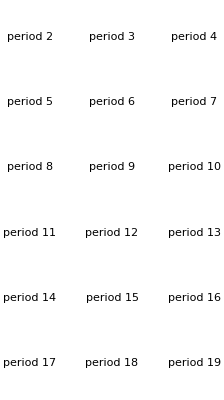

```mathematica
GraphicsGrid[Partition[
Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[ListPlot[Callout[{#Year, .25}, CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, #Period, ImageSize->3 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]], Top]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{{1969,2025},{0, 3}}, PlotStyle->PointSize[.025]], Text["period "<>ToString[i]<>"  "], Top]],{i,2, 20}], 3]]
```

#### GPT

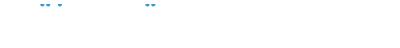
{-Graphics-
-Graphics-Period 2  
-Graphics-
-Graphics-Period 3  
-Graphics-
-Graphics-Period 4  
-Graphics-
-Graphics-Period 5  
-Graphics-
-Graphics-Period 6  
-Graphics-
-Graphics-Period 7  
-Graphics-
-Graphics-Period 8  
-Graphics-
-Graphics-Period 9  
-Graphics-
-Graphics-Period 10  
-Graphics-
-Graphics-Period 11  
-Graphics-
-Graphics-Period 12  ,-Graphics-
-Graphics-Period 13  
-Graphics-
-Graphics-Period 14  
-Graphics-
-Graphics-Period 15  
-Graphics-
-Graphics-Period 16  
-Graphics-
-Graphics-Period 17  
-Graphics-
-Graphics-Period 18  
-Graphics-
-Graphics-Period 19  
-Graphics-
-Graphics-Period 20  }

```mathematica
Column[Table[Module[{weightsovertime,improvements,locs,p=i,sortedData},sortedData=SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@sortedData;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Flatten[Position[Partition[improvements,2,1],{x_,y_}/;x!=y]];
(*Generate the labeled images and number line together*)Labeled[Column[{GraphicsRow[Table[With[{data=sortedData[[idx]]},Labeled[CellularAutomatonHistoryPlot["GameOfLife",{data["MatrixData"],0},data["Period"],ImageSize->3 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{data["MatrixData"],0},data["Period"]]]],Mesh->True,MeshStyle->Opacity[.1]],Text[data["Year"]],BaselinePosition->Top]],{idx,locs}]],(*Number line with images as callouts*)NumberLinePlot[Table[With[{data=sortedData[[idx]],img=CellularAutomatonHistoryPlot["GameOfLife",{sortedData[[idx]]["MatrixData"],0},sortedData[[idx]]["Period"],ImageSize->Small,Mesh->True,MeshStyle->Opacity[.1]]},Callout[data["Year"],img,Top]],{idx,locs}],Axes->None,PlotRange->{1969,2025}]}],Text["Period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{Range[2,12],Range[13,20]}
```

```mathematica
ListPlot[{Callout[Graphics[Rectangle[{0, 0}, {1, 1}]],Graphics@Rectangle[{3, 3}, {4, 4}] ]}]
```

-Graphics-

```mathematica
Graphics[{Callout[Rectangle[{0, 0}, {1, 1}],Rectangle[{3, 3}, {4, 4}] ]}]
```

-Graphics-

#### This is too fucking hard I’m moving on

### Histogram

```mathematica
Module[{ru = {299459058088077823758143088095350287424,4,1}},
lts200 = {{"[◼]", "TestCALifeTime"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{200,{-200,200}},#]]&/@{{"[◼]", "allperts"}}[CellularAutomaton[ru,{{1},0},{200,{-200,200}}]]];
```

```mathematica
ltsn = Table[ParallelTable[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[424324+i];{{"[◼]", "TestCALifeTime"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{200,{-200,200}},n]]],{i,10000}], {n, {2, 3, 5}}];
```

```mathematica
Module[{ru = {299459058088077823758143088095350287424,4,1}, ops = {{2},"Probability",Frame->True,FrameTicks->{Automatic,None},ImageSize->300, AspectRatio->.4}},
Grid[{{Histogram[lts200,Sequence@@Append[ops, Epilog->Text["1 perturbation",Scaled[{.85,.9}]]]],
Spacer[15],
Histogram[ltsn[[1]], Sequence@@Append[ops, Epilog->Text["2 perturbations",Scaled[{.85,.9}]]]]},
{Labeled[Histogram[ltsn[[2]],Sequence@@Join[ops, {Epilog->Text["3 perturbations",Scaled[{.85,.9}]]}]], Text[Style["lifetime", Medium]]],
Spacer[15],
Labeled[Histogram[ltsn[[3]],Sequence@@Join[ops, {Epilog->Text["5 perturbations",Scaled[{.85,.9}]]}]], Text[Style["lifetime", Medium]]]}}]]
```